```mathematica
(* Error can be broken into a product of two parts, part I coming from [0,(i-1)/n] and [(i+1)/n,1],
∫ Subscript[E, 1] * ∑ Subscript[E, 2]*)
```

```mathematica
(* Error from [0,(i-1)/n] *)
```

```mathematica
f1[n_,k_,a_,g_]:=(1 - Exp[(-2 n)/(k-1)a (g-x1)])PDF[NormalDistribution[0,√((k-1)/n)],x1](g-x1)PDF[NormalDistribution[0,1/(√n)],x1 - g]
```

```mathematica
(* Surivival probability of BM with linear boundary a+bt in time interval [0,T]*)
```

```mathematica
survivalprob[a_,b_,T_]:= CDF[NormalDistribution[],b √T+ a/(√T)] - ⅇ^(- 2 a b)CDF[NormalDistribution[],b √T- a/(√T)]
```

```mathematica
survivalprob[a,0,1]//FullSimplify
```

Erf[a/(√2)]

```mathematica
Manipulate[Plot[survivalprob[a,b,T],{T,0,1},PlotRange->{{0,1},{0,1}}],{a,0.2,3},{b,0,3}]
```

```mathematica
(* Error from [(i+1)/n,1]. As n->∞ and k->1, *)
```

```mathematica
f2[n_,k_,a_,g_]:=survivalprob[g-x2,0,(1 - (k+1)/n)](g-x2)PDF[NormalDistribution[0,1/(√n)],x2 - g]
```

```mathematica
f1list =Table[NIntegrate[f1[30,k,1,1],{x1,-∞,1}],{k,2,29}]
```

{0.000427284,0.00283346,0.00642357,0.00973043,0.0122042,0.0138418,0.0148093,0.0152856,0.015418,0.0153166,0.0150602,0.0147044,0.0142877,0.0138369,0.0133703,0.0129002,0.0124351,0.0119805,0.01154,0.0111156,0.0107085,0.0103191,0.00994763,0.00959365,0.0092567,0.00893615,0.00863129,0.00834139}

```mathematica
f2list =Table[NIntegrate[f2[30,k,1,1],{x2,-∞,1}],{k,1,28}]
```

{0.0135254,0.0137648,0.0140174,0.0142844,0.0145673,0.0148677,0.0151875,0.0155288,0.0158942,0.0162868,0.0167099,0.0171677,0.0176655,0.0182091,0.0188063,0.0194664,0.0202012,0.0210261,0.021961,0.0230329,0.0242789,0.0257516,0.0275296,0.0297354,0.0325735,0.0364183,0.0420522,0.0515032}

```mathematica
f12list = Table[NIntegrate[f1[30,k,1,1],{x1,-∞,1}]*NIntegrate[f2[30,k,1,1],{x2,-∞,1}],{k,2,28}]
```

{5.88149×10^-6,0.0000397177,0.000091757,0.000141746,0.000181448,0.000210222,0.00022997,0.000242953,0.00025111,0.000255938,0.00025855,0.00025976,0.000260167,0.000260221,0.000260271,0.0002606,0.000261462,0.000263105,0.0002658,0.000269873,0.00027576,0.000284082,0.000295797,0.000312499,0.000337113,0.000375785,0.000444539}

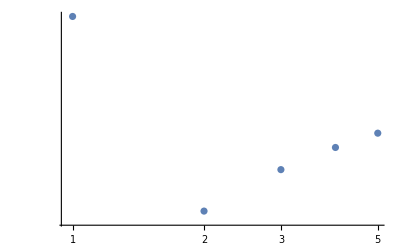

```mathematica
ListLogLogPlot[
Table[n*Total[Table[NIntegrate[f1[n,k,1,1],{x1,-∞,1}]*NIntegrate[f2[n,k,1,1],{x2,-∞,1}],{k,2,n-2}]]
+NIntegrate[f2[n,1,1,1],{x2,-∞,1}]
+NIntegrate[f1[n,n-1,1,1],{x1,-∞,1}]
,{n,5,500,100}]]
```

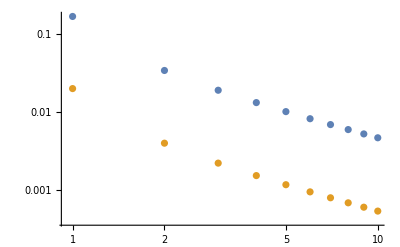

```mathematica
ListLogLogPlot[{
Table[
Total[Table[NIntegrate[f1[n,k,1,1],{x1,-∞,1}]*NIntegrate[f2[n,k,1,1],{x2,-∞,1}],{k,2,n-2}]]
+NIntegrate[f2[n,1,1,1],{x2,-∞,1}]
+NIntegrate[f1[n,n-1,1,1],{x1,-∞,1}]
,{n,5,200,20}],
Table[0.1/n,{n,5,200,20}]}]
```

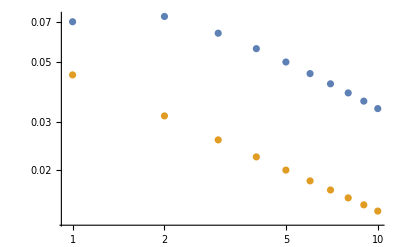

```mathematica
ListLogLogPlot[{Table[Total[Table[NIntegrate[f1a[n,k,1,1],{x,-∞,1}]*NIntegrate[f2[n,k,1,1],{x,-∞,1}],{k,2,n-2}]],{n,5,50,5}],Table[0.1/(√n),{n,5,50,5}]}]
```

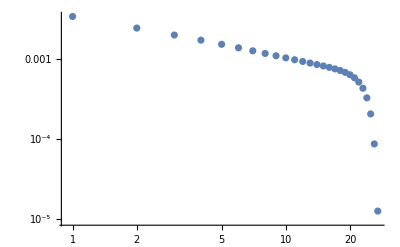

```mathematica
ListLogLogPlot[f12list]
```

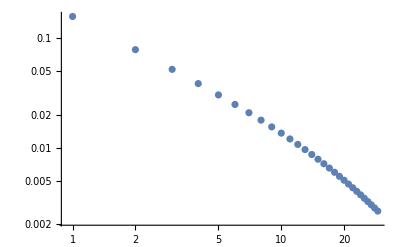

```mathematica
ListLogLogPlot[{ Table[
NIntegrate[f1a[30,k,3,1],{x,-∞,1}]*
NIntegrate[f1a[30,k,3,1],{x,-∞,1}],{k,2,30}]}]
```

```mathematica
xlista =Table[NIntegrate[f1a[30,k,1,1],{x,-∞,1}],{k,3,27}]
```

{0.273504,0.215956,0.179619,0.153689,0.133955,0.118335,0.10564,0.0951168,0.0862604,0.0787134,0.0722146,0.0665683,0.0616239,0.0572642,0.0533963,0.0499454,0.046851,0.0440635,0.0415418,0.0392517,0.0371645,0.0352558,0.033505,0.0318943,0.0304086}

```mathematica
ylist = Table[1/n,{n,30}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22,1/23,1/24,1/25,1/26,1/27,1/28,1/29,1/30}

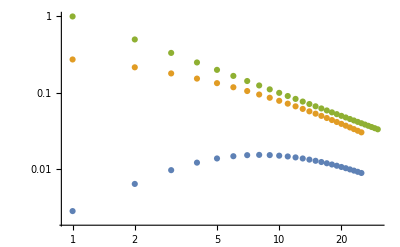

```mathematica
ListLogLogPlot[{xlist,xlista,ylist}]
```

```mathematica
Manipulate[ListLogLogPlot[{Table[NIntegrate[f1[n,k, 1, 1],{x,-∞,1}],{n,1,M}],Table[1/n,{n,1,M}] ,Table[(√n)/(k-1)^(3/2),{n,1,M}] } ],{M,3,40,1},{k,2,M,1}]
```

NIntegrate::inumr: The integrand f1[1, 2, 1, 1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NIntegrate::inumr: The integrand f1[2, 2, 1, 1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NIntegrate::inumr: The integrand f1[3, 2, 1, 1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand f1[1,2,1,1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,1.}}.

NIntegrate::inumr: The integrand f1[2,2,1,1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,1.}}.

NIntegrate::inumr: The integrand f1[3,2,1,1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
(* Fixed n, plot from i = 2 to n*)
```

```mathematica
Manipulate[ListPlot[{Table[NIntegrate[f1[n,k, 9, 1],{x,-∞,1}],{k,2,n}],Table[NIntegrate[f1[n,k, 1, 1],{x,-∞,1}],{k,2,n}]}],{n,3,80,1}]
```

```mathematica
Manipulate[ListLogLogPlot[{Table[NIntegrate[f2[n,i,1,1],{x,-∞,1}],{n,1,M}],Table[1/n,{n,1,M}] } ],{M,3,40,1},{i,2,M,1}]
```

```mathematica
f2[31,13,1,1]
```

(31 ⅇ^(-31/2 (-1+x)^2-(31 x^2)/34) (1-ⅇ^(-62/17 (1-x))) (1-x))/(2 √17 π)

```mathematica
∫_(-∞)^1 f2[31,13,1,1]ⅆx
```

(√(31/π))/(108 ⅇ^(31/36))

```mathematica
∫_(-∞)^g (1 - Exp[-2/(1 - (i+1)/n)g(g-x)])/(√(2π (1 - (i+1)/n)))Exp[-x^2/(2(1 - (i+1)/n))](g-x)PDF[NormalDistribution[0,1/(√n)],x - g]ⅆx
```

$Aborted